## 1.1.:

```mathematica
Get["C:\\Users\\Marko\\Documents\\Faks\\Faks\\Napredna Računalniška Orodja\\Rac_Pi.m"]
Rač= Račun[69420];
```

```mathematica
RačPi = Rač[[1]]
KoZun = Rač[[2]];
KoNot = Rač[[3]];
```

3.14578

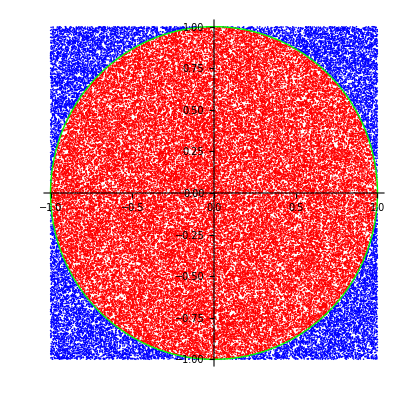

```mathematica
p1 = ListPlot[KoNot, PlotStyle->Red];
p2 = ListPlot[KoZun, PlotStyle->Blue];
p3 = ParametricPlot[{Cos[t],Sin[t]},{t,0,2Pi},PlotStyle->{Green,Thick}];
Show[p1,p2,p3,AspectRatio->1,PlotRange->All]
```

## 1.2.:

```mathematica
f[t_] = Sin[t] t^2 E^-t
```

ⅇ^-t t^2 Sin[t]

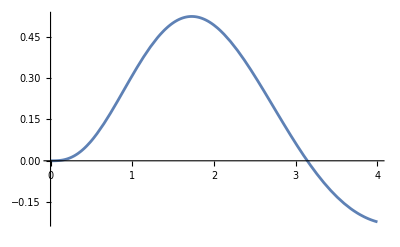

```mathematica
Plot[f[t],{t,0,4},PlotRange->All]
```

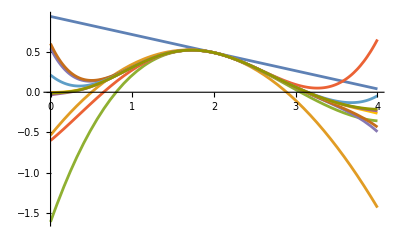

```mathematica
Clear[n,m]
m= Table[Normal[Series[f[t],{t,2,n}]],{n,1,10}];

Plot[m,{t,0,4},PlotRange->All]
```

```mathematica
Manipulate[Plot[{m[[n]],f[t]},{t,0,4},PlotRange->{{0,4},{-.5,1}},Filling->{1->{2}},FillingStyle->Yellow],{n,1,10,1}]
```